## Final Project: Mathematics of Musical Harmony Matthew McGowan

A Brief Aside on Playing Music in Mathematica

We have seen before that it is possible to create pure tones using sine waves. This is shown below.

```mathematica
Play[Sin[2 Pi 220 t],{t,0,2}]
```

-Graphics-

However, it is also possible to play midi instruments in Mathematica.

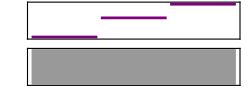

```mathematica
Sound[SoundNote[#,.5,"Piano"]&/@{0,7,12}]
```

You can also import midi files and play them.

/home/matthew/Desktop/Texts/MATH299M

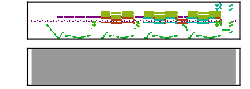

```mathematica
SetDirectory[NotebookDirectory[]]
Import["Seinfeld.mid"]
```

It seems that if you use any midi instruments other than just the basic piano, then you have to load something from the Mathematica servers before playing the audio.

Consonance and Dissonance

Harmony is simply when two notes are played at the same time. Why do some notes sound good together while some notes sound bad together? Consonance means that two notes sound “nice” together, while dissonance means two notes sound “bad” together.
Below is an example of the consonant octave and perfect fifth intervals, as well as the dissonant minor second.

These two notes sounds good together. (Perfect Octave)

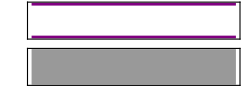

```mathematica
Sound[SoundNote[{0,12},2,"Piano"]]
```

These notes also sound good together. (Perfect Fifth)

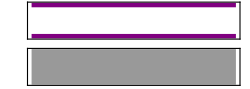

```mathematica
Sound[SoundNote[{0,7},2,"Piano"]]
```

But these two notes do not sound good together. (Minor Second)

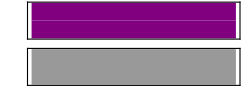

```mathematica
Sound[SoundNote[{0,1},2,"Piano"]]
```

Notation and Basics of Frequency-Note Mapping

In order to notate music, we assign note names (A, B, C, D, E , F, G) to different frequencies. When talking about specific notes, a subscript is used to talk about which octave of a note we are referring to. Middle C, or C_4, is the C note found in the middle of most keyboards. The C note below C_4 is denoted C_3 and the one above is denoted C_5. Subscript numbering starts with C and ends with D. So 1 whole step down from C_4 is D_3, while one whole step up from D_4 is C_5. A typical piano will have 88 keys and will range from A_0 to C_8.

Pianos are tuned so that the 49th piano key (A_4) is 440Hz. By going up a single half step from any note, meaning to go to the next adjacent key, whether it is a black key or white key, the frequency will be multiplied by ^12 √2 ≈ 1.0595. The frequency will be divided by the same amount for going down a single half step. (Note: This is true for equal-temperament tuning, but other tuning systems have been used in past, which use different tuning systems)

To go up one octave (e.g. C_4 to C_5, or F_2 to F_3), you must go up by 12 semitones. This will result in the frequency increasing by a factor of ^12(√2)^12, which is just 2. From this, we can see that octaves of the same notes correspond to harmonics of a given frequency. This is demonstrated in the visual below for a note X with octave n.

Octaves may be one of the most consonant intervals, because the ratio between frequencies is always a whole number.

Intervals and Ratios

```mathematica
Manipulate[Plot[{Sin[ Pi x],Sin[2 c Pi x]},{x,0,1},PlotRange->{-1,1},PlotLabel->Style["Octaves as Harmonics Visualized as a Wave on a String",16],PlotLegends->{"X_n","X_(n*SuperscriptBox[2, c])"/.y->2c},ImageSize->Large],{c,1,5,1}]
```

Two notes sounds “good” together when there is an “nice” integer ratio between their frequences. This is most easily seen for notes that are an octave apart (12 semitones), because the frequences differ by a factor of 2^(12/12), which is just 2.
But what about for other intervals, since 2^(1/12)raised to power of some other number won’t create a “nice” interval because they are irrational.

```mathematica
Grid[Prepend[Partition[Riffle[Table[x,{x,1,12}],Table[2^(x/12)//N,{x,1,12}]],2],{"Semitones","Decimal Approximation of Interval"}],Alignment->Left,Spacings->{2,1},Frame->All,FrameStyle->Directive[Black,Thin]]
```

Semitones | Decimal Approximation of Interval
1 | 1.05946
2 | 1.12246
3 | 1.18921
4 | 1.25992
5 | 1.33484
6 | 1.41421
7 | 1.49831
8 | 1.5874
9 | 1.68179
10 | 1.7818
11 | 1.88775
12 | 2.

None of these ratios are “nice” except for  12 semitones, whats the deal? Well it turns out that these numbers are actually pretty close to some ratios that are nice. (Notes with an asterisk next to their interval name indicate notes that would be out of scale for a major key relative to the root key.)

```mathematica
Grid[{{"Interval Name","Semitones","Accurate Approximation","\"Nice\" Approximation","\"Nice\" Ratio (Just Intonation)"},{"Minor Second*",1,2^(1/12)//N,16/15//N,"16/15"},{"Major Second",2,2^(2/12)//N,9/8//N,"9/8"},{"Minor Third*",3,2^(3/12)//N,6/5//N,"6/5"},{"Major Third",4,2^(4/12)//N,5/4//N,"5/4"},{"Perfect Fourth",5,2^(5/12)//N,4/3//N,"4/3"},{"Dim. Fifth/Tritone*",6,2^(6/12)//N,45/32//N,"45/32"},{"Perfect Fifth",7,2^(7/12)//N,3/2//N,"3/2"},{"Minor Sixth*",8,2^(8/12)//N,8/5//N,"8/5"},{"Major Sixth",9,2^(9/12)//N,5/3//N,"5/3"},{"Minor Seventh*",10,2^(10/12)//N,16/9//N,"16/9"},{"Major Seventh",11,2^(11/12)//N,15/8//N,"15/8"},{"Perfect Octave",12,2.,2.,"2/1"}},Alignment->Left,Spacings->{2,1},Frame->All,FrameStyle->Directive[Black,Thin]]
```

Interval Name | Semitones | Accurate Approximation | "Nice" Approximation | "Nice" Ratio (Just Intonation)
Minor Second* | 1 | 1.05946 | 1.06667 | 16/15
Major Second | 2 | 1.12246 | 1.125 | 9/8
Minor Third* | 3 | 1.18921 | 1.2 | 6/5
Major Third | 4 | 1.25992 | 1.25 | 5/4
Perfect Fourth | 5 | 1.33484 | 1.33333 | 4/3
Dim. Fifth/Tritone* | 6 | 1.41421 | 1.40625 | 45/32
Perfect Fifth | 7 | 1.49831 | 1.5 | 3/2
Minor Sixth* | 8 | 1.5874 | 1.6 | 8/5
Major Sixth | 9 | 1.68179 | 1.66667 | 5/3
Minor Seventh* | 10 | 1.7818 | 1.77778 | 16/9
Major Seventh | 11 | 1.88775 | 1.875 | 15/8
Perfect Octave | 12 | 2. | 2. | 2/1

It is also interesting to note that 6 semitones creates a ration of √2.

Consonance and Dissonance in Waveforms

Lets take a look at those intervals that we played earlier and see how that looks as waveforms. These example waveforms are actually the plots of a 1 Hz frequency and its accompanying interval frequency.
For the first two pairs of intervals, it is very easy to see how the frequencies “harmonize” and makes a clean wave.

```mathematica
Manipulate[Column[{Plot[{Sin[2 Pi x],Sin[2 2 Pi x]},{x,0,xlim},PlotRange->2,PlotPoints->40,PlotLabel->Style["Perfect Octave Interval (Seperate Waves)",16],PlotLegends->{"base freq","2 * base freq"},ImageSize->Large],
Plot[{Sin[ 2Pi x]+Sin[2 2 Pi x]},{x,0,xlim},PlotRange->2,PlotPoints->40,PlotLabel->Style["Perfect Octave Interval (Added Waves)",16],ImageSize->Large]}],{{xlim,2},2,32,.1}]
```

```mathematica
Manipulate[Column[{Plot[{Sin[2 Pi x],Sin[2^(7/12) 2 Pi x]},{x,0,xlim},PlotRange->2,PlotPoints->40,PlotLabel->Style["Perfect Fifth Interval (Seperate Waves)",16],PlotLegends->{"base freq","~3/2 * base freq"},ImageSize->Large],
Plot[{Sin[ 2Pi x]+Sin[2^(7/12) 2 Pi x]},{x,0,xlim},PlotRange->2,PlotPoints->40,PlotLabel->Style["Perfect Fifth Interval (Added Waves)",16],ImageSize->Large]}],{{xlim,2},2,32,.1}]
```

For this next plot, which showcases the minor second. It is easily seen how the two waves do not line up as neatly as the other intervals we looked at above. We actually need to “zoom out” pretty far before we see what is really going on.

```mathematica
Manipulate[Column[{Plot[{Sin[2 Pi x],Sin[2^(1/12) 2 Pi x]},{x,0,xlim},PlotRange->2,PlotPoints->40,PlotLabel->Style["Minor Second Interval (Seperate Waves)",16],PlotLegends->{"base freq","~16/15 * base freq"},ImageSize->Large],
Plot[{Sin[ 2Pi x]+Sin[2^(1/12) 2 Pi x]},{x,0,xlim},PlotRange->2,PlotPoints->40,PlotLabel->Style["Minor Second Interval (Added Waves)",16],ImageSize->Large]}],{{xlim,2},2,32,.1}]
```

Beat Waves

In the above example showing the minor second interval, you can clearly the what is known as a “beat”, which is a interference pattern that occurs when two waves have a slightly different frequency. This can be perceived as a periodic variation in pattern. This can be modeled as the envelope of the added waves. The frequency of the beat is half of the difference between the two frequencies.
Below is an auditory example of a beat.

```mathematica
Play[Sin[2 Pi 110 t],{t,0,2}]
Play[Sin[2Pi 104 t],{t,0,2}]
Play[Sin[2 Pi 110 t]+Sin[2 Pi 104 t],{t,0,2}]
```

-Graphics-

-Graphics-

-Graphics-

A More Manipulable Manipulate

Here we can see how the beat wave develops as the interval between frequencies change.

```mathematica
Manipulate[Column[{Plot[{Sin[2 Pi x],Sin[2^(c/12) 2 Pi x]},{x,0,xlim},PlotRange->2,PlotPoints->40,PlotLabel->Style["Seperate Waves",16],ImageSize->Large],
Plot[{Sin[ 2Pi x]+Sin[2^(c/12) 2 Pi x],2 Cos[1/2(Abs[1-2^(c/12)])2 Pi x],-2 Cos[1/2(Abs[1-2^(c/12)])2 Pi x]},{x,0,xlim},PlotRange->2,PlotPoints->40,PlotLabel->Style["Added Waves",16],PlotStyle->{Opacity[1],{Opacity[beat],Thickness[.005]},{Opacity[beat],Thickness[.005]}},ImageSize->Large]}],{{xlim,2},2,32,.1},{{c,1,"Multiplier"},0,24,.1},{{beat,0,"Beat Wave"},{1,0}}]
```

“Visual Dissonance” in Moiré Patterns

The auditory phenomenon of beats is a parallel to the visual phenomenon of Moiré patterns, which is a visual interference pattern which can be caused by two sets of many parallel lines, where one is at a slight angle or when the two sets have different widths between lines (similar to two waves having different wave lengths).

```mathematica
Manipulate[lines=Table[Line[{{x,-1},{x,1}}],{x,-1,1,.02}];Graphics[{lines,Rotate[lines,θ]}],{θ,0,Pi/4}]
Manipulate[Graphics[{Table[Line[{{x,-1},{x,.5}}],{x,-1,1,.02}],Table[Line[{{x,-.5},{x,1}}],{x,-1,1,.02+Δ}]}],{Δ,0,.01}]
Manipulate[Graphics[{Table[Line[RotationMatrix[θ]*{{1,-1},{0,0}}],{θ,0,2 Pi,.03}],Table[Line[RotationMatrix[θ]*{{1,-1},{0,0}}-{{Δ,0},{Δ,0}}],{θ,0,2 Pi,.03}]}],{Δ,0,1}]
```

Sources:

http://www.animations.physics.unsw.edu.au/jw/beats.htm
http://newt.phys.unsw.edu.au/jw/musFAQ.html#Tartini
http://www.mathscareers.org.uk/article/harmony-numbers/
https://en.wikipedia.org/wiki/Beat_(acoustics)
https://en.wikipedia.org/wiki/Consonance_and_dissonance
https://en.wikipedia.org/wiki/Equal_temperament
https://en.wikipedia.org/wiki/Harmonic
https://en.wikipedia.org/wiki/Interval_(music)
https://en.wikipedia.org/wiki/Interval_ratio
https://en.wikipedia.org/wiki/Just_intonation
https://en.wikipedia.org/wiki/Moir%C3%A9_pattern
https://en.wikipedia.org/wiki/Piano_key_frequencies
https://en.wikipedia.org/wiki/Pythagorean_tuning
https://reference.wolfram.com/language/guide/SoundAndSonification.html
https://reference.wolfram.com/language/ref/SoundNote.html
https://reference.wolfram.com/language/ref/format/MIDI.html